```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy485-optics"]
```

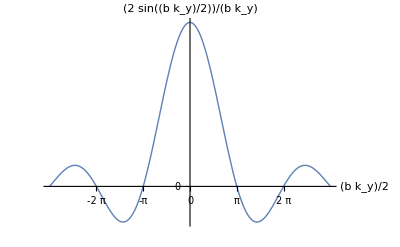

```mathematica
fs = Style[#, FontSize->14]&;

lecture15figuresSincCrossingsFig7 = Plot[ Sin[x]/(x), 
{x, -3 Pi, 3 Pi},
Ticks -> {{ -2 Pi, -Pi, 0,  Pi,  2 Pi}},
AxesLabel -> { b Subscript[k, y]/2 // fs, Sin[ b Subscript[k, y]/2]/(b Subscript[k, y]/2) // fs},
PlotStyle->Thick
]
```

```mathematica
Manipulate[
Module[
{beta, gamma, k},
k = 2 Pi (*/ (650 10^(-9))*) ;
beta = b k Sin[theta] /2 ;
gamma = a k Sin[theta]/2 ;
Plot[ (Sin[beta]/beta)^2 (Sin [n gamma]/ Sin[gamma])^2, {theta, -Pi, Pi}
, PlotRange -> Full
, PlotStyle-> Thick]
],
{{b, 0.172}, 0.01, 1},
{{a, 0.869}, 0.01, 1},
{{n, 5}, 1, 30, 1}
]
```

```mathematica
lecture15figures5aperaturesIntensityPlotFig8 = DynamicModule[{a=0.869,b=0.172,n=5},Module[{beta$,gamma$,k$},k$=2 π;beta$=1/2 b k$ Sin[theta];gamma$=1/2 a k$ Sin[theta];Plot[(Sin[beta$]/beta$)^2 (Sin[n gamma$]/Sin[gamma$])^2,{theta,-π,π},PlotRange->Full,PlotStyle->Thick]]]
```

```mathematica
peeters`exportForLatex["lecture15figuresSincCrossingsFig7",lecture15figuresSincCrossingsFig7]
```

{lecture15figuresSincCrossingsFig7.eps,lecture15figuresSincCrossingsFig7pn.png}

```mathematica
peeters`exportForLatex["lecture15figures5aperaturesIntensityPlotFig8",lecture15figures5aperaturesIntensityPlotFig8]
```

{lecture15figures5aperaturesIntensityPlotFig8.eps,lecture15figures5aperaturesIntensityPlotFig8pn.png}